{0,0,10,12,30,24,20,18,19,15,0,0,0,2}

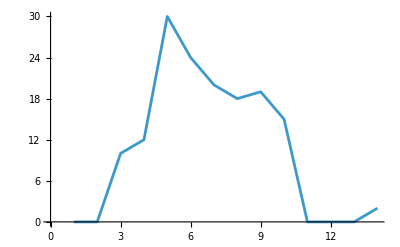

```mathematica
l1={0,0,10,12,30,24,20,18,19,15,0,0,0,2}
ListLinePlot[l1]
```

```mathematica
FindPeaks[l1]
```

{{5,30},{14,2}}

```mathematica
cwt12=ContinuousWaveletTransform[l1,MexicanHatWavelet[1],{2,4}]
```

ContinuousWaveletData[…]

```mathematica
cwt14=ContinuousWaveletTransform[l1,MexicanHatWavelet[1],{4,4}]
```

ContinuousWaveletData[…]

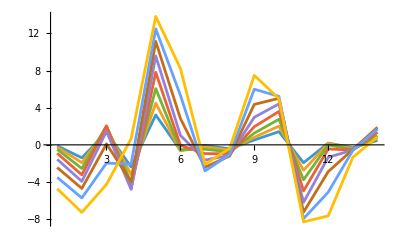

```mathematica
ListLinePlot[cwt12[All,"Values"]//Re,PlotRange->Full]
```

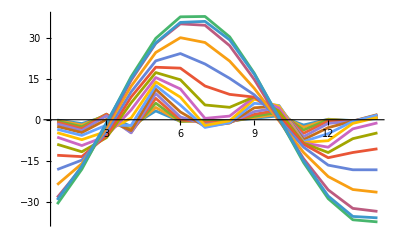

```mathematica
ListLinePlot[cwt14[All,"Values"]//Re,PlotRange->Full]
```

```mathematica
cwt12[All,"Values"][[8]]
```

{-4.72526-3.70159×10^-16 ⅈ,-7.26974-1.37372×10^-16 ⅈ,-4.26282-2.43198×10^-16 ⅈ,0.660352-1.96943×10^-16 ⅈ,13.8243+2.36327×10^-16 ⅈ,8.23601-6.83386×10^-17 ⅈ,-2.09672+2.59215×10^-16 ⅈ,-0.37624+2.97255×10^-16 ⅈ,7.47942+6.08131×10^-17 ⅈ,4.97986+2.97255×10^-16 ⅈ,-8.29551+1.26222×10^-16 ⅈ,-7.65297-6.83386×10^-17 ⅈ,-1.33551+4.20477×10^-18 ⅈ,0.834854-1.96943×10^-16 ⅈ}

```mathematica
cwt14[All,"Values"][[8]]
```

{-4.72526-3.70159×10^-16 ⅈ,-7.26974-1.37372×10^-16 ⅈ,-4.26282-2.43198×10^-16 ⅈ,0.660352-1.96943×10^-16 ⅈ,13.8243+2.36327×10^-16 ⅈ,8.23601-6.83386×10^-17 ⅈ,-2.09672+2.59215×10^-16 ⅈ,-0.37624+2.97255×10^-16 ⅈ,7.47942+6.08131×10^-17 ⅈ,4.97986+2.97255×10^-16 ⅈ,-8.29551+1.26222×10^-16 ⅈ,-7.65297-6.83386×10^-17 ⅈ,-1.33551+4.20477×10^-18 ⅈ,0.834854-1.96943×10^-16 ⅈ}

{0,0,10,12,30,40,60,100,110,111}

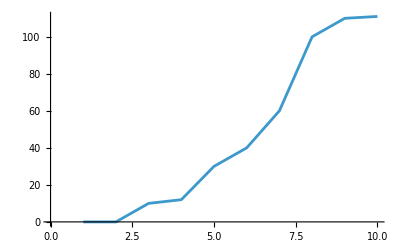

```mathematica
l2={0,0,10,12,30,40,60,100,110,111}
ListLinePlot[l2]
```

```mathematica
FindPeaks[l2]
```

{{10,111}}

```mathematica
cwt2=ContinuousWaveletTransform[l2,MexicanHatWavelet[1],{3,4}]
```

ContinuousWaveletData[…]

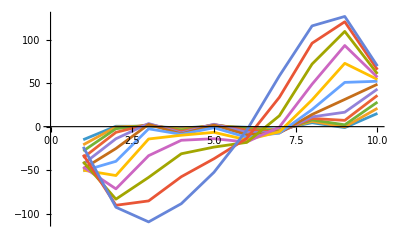

```mathematica
ListLinePlot[cwt2[All,"Values"]]
```

{0.778464,0.314148,0.126693,0.0496936,0.75841,0.722929,0.372594,0.249244,0.982669,0.692078}

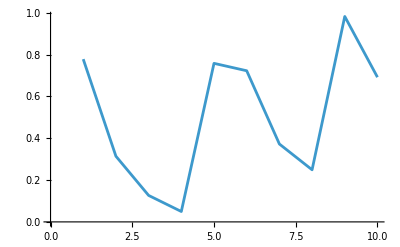

```mathematica
lr=Table[RandomReal[],{10}]
ListLinePlot[lr]
```

```mathematica
cwtr=ContinuousWaveletTransform[lr,MexicanHatWavelet[1]]
```

ContinuousWaveletData[…]

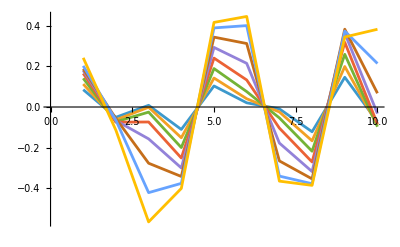

```mathematica
ListLinePlot[cwtr[All,"Values"]]
```

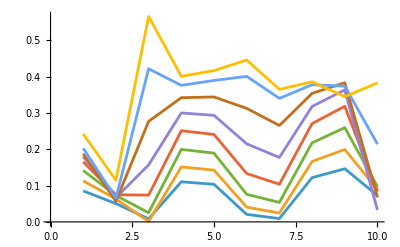

```mathematica
Map[Abs,cwtr[All,"Values"]]//ListLinePlot
```

```mathematica
Map[Norm,cwtr[All,"Values"],{-1}]//ListLinePlot
```

-Graphics-

```mathematica
Map[Re,cwtr[All,"Values"],{-1}]//ListLinePlot
```

-Graphics-

```mathematica
base={0,0,0,0,1.2,1.6,2.4,1.8,1,0,0,0,0,0,0.8,.6,1.4,1.2,0.6,0,0,0,0.3,0.2,0.4,0.2,0.2,0.1,0,0,0,0,0,0,0,0.2,0,0,0,0}*2
```

{0,0,0,0,2.4,3.2,4.8,3.6,2,0,0,0,0,0,1.6,1.2,2.8,2.4,1.2,0,0,0,0.6,0.4,0.8,0.4,0.4,0.2,0,0,0,0,0,0,0,0.4,0,0,0,0}

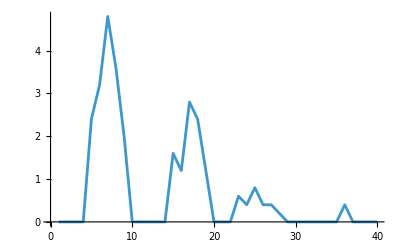

```mathematica
ListLinePlot[base]
```

```mathematica
Length[base]
```

40

```mathematica
lr40=(Table[RandomReal[],{40}]+0.2)*0.8+base
```

{0.612399,0.394324,0.592603,0.786603,2.8784,3.67827,5.52043,4.12605,2.70559,0.45982,0.458119,0.265263,0.675792,0.876215,2.42557,1.77894,3.66292,3.34879,2.15659,0.503043,0.513813,0.686351,0.980648,0.790527,1.68954,0.761807,0.617299,0.556601,0.928284,0.503198,0.21209,0.744986,0.269801,0.223213,0.568048,1.04589,0.168619,0.380601,0.793507,0.29686}

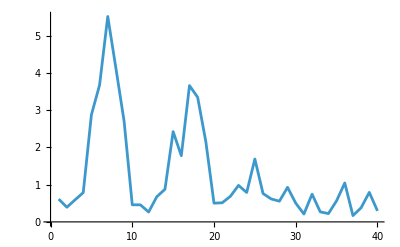

```mathematica
ListLinePlot[lr40]
```

```mathematica
FindPeaks[lr40]
```

{{1,0.612399},{7,5.52043},{17,3.66292},{25,1.68954},{29,0.928284},{32,0.744986},{36,1.04589},{39,0.793507}}

```mathematica
cwtr40=ContinuousWaveletTransform[lr40,MexicanHatWavelet[1]]
```

ContinuousWaveletData[…]

ピーク推定

モジュール読み込み：

```mathematica
Get["/Users/kouamano/gitsrc/SCRIPT_Mathematica/SCRIPTS/Wavelet.txt"]
```

```mathematica
cwt12[All,"Values"]//WTPE
```

2

```mathematica
WTPE[cwt12[All,"Values"],"position"]
```

{{5},{9},{10}}

```mathematica
cwtr[All,"Values"]
```

{{0.0854797+0. ⅈ,-0.0504952+0. ⅈ,0.00829036-1.63143×10^-18 ⅈ,-0.110494+3.26286×10^-18 ⅈ,0.103648+2.63971×10^-18 ⅈ,0.0207039-5.27942×10^-18 ⅈ,-0.00914804-2.63971×10^-18 ⅈ,-0.121945+5.27942×10^-18 ⅈ,0.146454+1.63143×10^-18 ⅈ,-0.0724934-3.26286×10^-18 ⅈ},{0.113089+1.11022×10^-17 ⅈ,-0.0633026+0. ⅈ,-0.00110239-1.22448×10^-17 ⅈ,-0.151563+3.26286×10^-18 ⅈ,0.142725+8.7102×10^-18 ⅈ,0.0406392-5.27942×10^-18 ⅈ,-0.0243689-1.84865×10^-18 ⅈ,-0.166495+5.27942×10^-18 ⅈ,0.199519-5.71903×10^-18 ⅈ,-0.0891412-3.26286×10^-18 ⅈ},{0.141506+1.11022×10^-17 ⅈ,-0.0728568+2.77556×10^-18 ⅈ,-0.0251406-9.60504×10^-18 ⅈ,-0.199818+1.16546×10^-17 ⅈ,0.189444+1.03416×10^-17 ⅈ,0.0759729-1.38126×10^-17 ⅈ,-0.0537478-3.48008×10^-18 ⅈ,-0.217904+9.32166×10^-18 ⅈ,0.259669-8.35874×10^-18 ⅈ,-0.0971246-9.93918×10^-18 ⅈ},{0.165375+0. ⅈ,-0.0746932+2.22045×10^-17 ⅈ,-0.0738663-6.52573×10^-18 ⅈ,-0.251263-8.1752×10^-18 ⅈ,0.241028+1.05588×10^-17 ⅈ,0.133257-8.97672×10^-18 ⅈ,-0.103926-1.05588×10^-17 ⅈ,-0.270885+2.26998×10^-17 ⅈ,0.318636+6.52573×10^-18 ⅈ,-0.0836618-2.77524×10^-17 ⅈ},{0.180021+2.22045×10^-17 ⅈ,-0.0669246+1.38778×10^-18 ⅈ,-0.157022-2.44895×10^-17 ⅈ,-0.300244+9.59429×10^-18 ⅈ,0.293652+1.74204×10^-17 ⅈ,0.215164-1.00502×10^-17 ⅈ,-0.177664-3.69729×10^-18 ⅈ,-0.318162+7.80468×10^-18 ⅈ,0.363891-1.14381×10^-17 ⅈ,-0.0327112-8.73659×10^-18 ⅈ},{0.187764+2.22045×10^-17 ⅈ,-0.0569386+4.44089×10^-17 ⅈ,-0.277081-3.10152×10^-17 ⅈ,-0.342318-1.96133×10^-17 ⅈ,0.344331+2.79793×10^-17 ⅈ,0.312887-1.2674×10^-17 ⅈ,-0.265629-1.42561×10^-17 ⅈ,-0.354239+4.01202×10^-17 ⅈ,0.383524-4.91233×10^-18 ⅈ,0.0676999-5.22419×10^-17 ⅈ},{0.202767+0. ⅈ,-0.0653357+4.71845×10^-17 ⅈ,-0.422013-6.52573×10^-18 ⅈ,-0.376309-2.69127×10^-17 ⅈ,0.38975+1.05588×10^-17 ⅈ,0.401105-1.72092×10^-18 ⅈ,-0.340453-1.05588×10^-17 ⅈ,-0.378048+2.46762×10^-17 ⅈ,0.374131+6.52573×10^-18 ⅈ,0.214405-4.3227×10^-17 ⅈ},{0.242372,-0.11472,-0.566182,-0.401257,0.416935,0.446224,-0.365325,-0.386115,0.345004,0.383065}}

```mathematica
WTPE[cwtr[All,"Values"]]
```

2

```mathematica
WTPE[cwtr[All,"Values"],"position"]
```

{{5},{6},{9}}

```mathematica
WTPE[cwtr40[All,"Values"]]
```

2

```mathematica
WTPE[cwtr40[All,"Values"],"position"]//Flatten
```

{7,17,18,19}

```mathematica
mergePkPos[WTPE[cwtr40[All,"Values"],"position"]//Flatten]
```

{{7},{17,18,19}}